```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\Critical-region\QCD\v1\delta\source

```mathematica
fpi=Flatten[Table[Import["./Tem"<>ToString[i]<>"/BUFFER/FPI.DAT"],{i,1,100}]];
Zphi=Flatten[Table[Import["./Tem"<>ToString[i]<>"/BUFFER/ZPHI.DAT"],{i,1,100}]];
fpi0=fpi(*/√Zphi*);
h=Flatten[Table[Import["./Tem"<>ToString[i]<>"/BUFFER/H.DAT"],{i,1,100}]];
(*h=h*√Zphi;*)
data=Transpose[{h,fpi}];
```

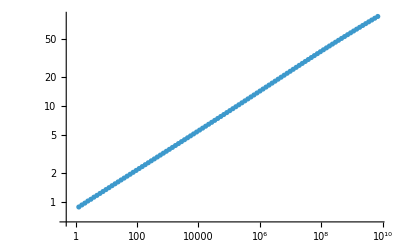

```mathematica
ListPlot[data,ScalingFunctions->{"Log","Log"}]
```

```mathematica
datalog=Transpose[{Log[h],Log[fpi0]}];
```

```mathematica
slop=Table[FindFit[datalog[[i;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,1,99}];
```

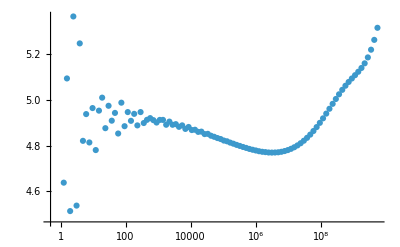

```mathematica
ListPlot[Transpose[{h[[1;;99]],1/slop}],ScalingFunctions->{"Log"}]
```

```mathematica
c0data=Flatten[Import["c0data1.dat"]];
sigmadata=Flatten[Import["sigmadata1.dat"]];
c0data2=Flatten[Import["c0data2.dat"]];
sigmadata2=Flatten[Import["sigmadata2.dat"]];
(*olddata=Transpose[{Log[c0data],Log[sigmadata]}];
olddata2=Transpose[{Log[c0data2],Log[sigmadata2]}];*)
sigmaall=Flatten[{sigmadata,sigmadata2}];
c0all=Flatten[{c0data,c0data2}];
dataall=Transpose[{Log[c0all],Log[sigmaall]}];
slop1=Table[FindFit[dataall[[i;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,1,Length[c0all]-1}];
```

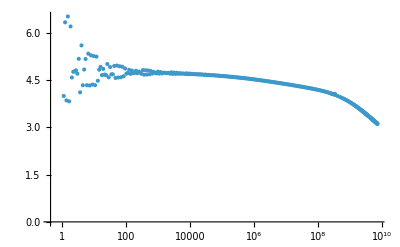

```mathematica
ListPlot[{Transpose[{c0all[[1;;-2]],1/slop1}]},ScalingFunctions->{"Log"}]
```

```mathematica
delta=4.7842049914123224184691716988644852126802550618815156961252`40.;
Block[{Bc12,am12,thetaH=0.272`40},{Bc12,am12}={Bc,am}/.NonlinearModelFit[{Transpose[(SetPrecision[ListΔc3[31,75],80]//Log)][[1]],Transpose[(SetPrecision[ListΔc3[31,75],80]//Log)][[2]]}//Transpose,lgbc+Log[1+am ⅇ^(lgx thetaH)]+lgx/delta43,{lgbc,am},lgx,MaxIterations->400]["BestFitParameters"];ParallelTable[Clear[cfa,cfb,na,nb,xadata,xbdata,yadata,ybdata];
{1/invδ,am12,mpi[[i]]}/.NonlinearModelFit[Transpose[{csigmabar3[[i-4;;i+4]]//Log,(SetPrecision[deltalbar3[[i-4;;i+4]],80]//Log)-Log[1+am12 ⅇ^(Log[SetPrecision[csigmabar3,80]] thetaH)][[i-4;;i+4]]}],lgx*invδ+lgbc,{lgbc,invδ},lgx,MaxIterations->400]["BestFitParameters"],{i,11,280,1}]];
```

{{0.0980579,-9.06203-Log[1+am]},{0.196116,-9.03753-Log[1+am]},{0.294174,-9.02207-Log[1+am]},{0.392231,-8.99668-Log[1+am]},{0.490289,-8.98166-Log[1+am]},{0.588347,-8.95607-Log[1+am]},{0.686405,-8.94028-Log[1+am]},{0.784463,-8.91892-Log[1+am]},{0.882521,-8.89836-Log[1+am]},{0.980578,-8.87786-Log[1+am]},{1.07864,-8.8575-Log[1+am]},{1.17669,-8.83668-Log[1+am]},{1.27475,-8.81776-Log[1+am]},{1.37281,-8.79394-Log[1+am]},{1.47087,-8.77646-Log[1+am]},{1.56893,-8.75388-Log[1+am]},{1.66698,-8.73363-Log[1+am]},{1.76504,-8.71469-Log[1+am]},{1.8631,-8.69211-Log[1+am]},{1.96116,-8.67378-Log[1+am]},{2.05921,-8.65116-Log[1+am]},{2.15727,-8.63263-Log[1+am]},{2.25533,-8.61016-Log[1+am]},{2.35339,-8.59155-Log[1+am]},{2.45145,-8.56899-Log[1+am]},{2.5495,-8.55031-Log[1+am]},{2.64756,-8.52845-Log[1+am]},{2.74562,-8.50818-Log[1+am]},{2.84368,-8.48828-Log[1+am]},{2.94174,-8.46725-Log[1+am]},{3.03979,-8.44708-Log[1+am]},{3.13785,-8.42614-Log[1+am]},{3.23591,-8.40512-Log[1+am]},{3.33397,-8.38557-Log[1+am]},{3.43202,-8.36423-Log[1+am]},{3.53008,-8.3443-Log[1+am]},{3.62814,-8.32339-Log[1+am]},{3.7262,-8.30248-Log[1+am]},{3.82426,-8.28269-Log[1+am]},{3.92231,-8.26126-Log[1+am]},{4.02037,-8.24153-Log[1+am]},{4.11843,-8.22015-Log[1+am]},{4.21649,-8.20033-Log[1+am]},{4.31455,-8.179-Log[1+am]},{4.4126,-8.15911-Log[1+am]},{4.51066,-8.13793-Log[1+am]},{4.60872,-8.11781-Log[1+am]},{4.70678,-8.09699-Log[1+am]},{4.80483,-8.07627-Log[1+am]},{4.90289,-8.05598-Log[1+am]},{5.00095,-8.03513-Log[1+am]},{5.09901,-8.01475-Log[1+am]},{5.19707,-7.994-Log[1+am]},{5.29512,-7.9733-Log[1+am]},{5.39318,-7.95288-Log[1+am]},{5.49124,-7.93213-Log[1+am]},{5.5893,-7.9116-Log[1+am]},{5.68735,-7.89094-Log[1+am]},{5.78541,-7.87011-Log[1+am]},{5.88347,-7.84978-Log[1+am]},{5.98153,-7.82882-Log[1+am]},{6.07959,-7.80848-Log[1+am]},{6.17764,-7.78755-Log[1+am]},{6.2757,-7.76717-Log[1+am]},{6.37376,-7.74627-Log[1+am]},{6.47182,-7.72582-Log[1+am]},{6.56988,-7.70503-Log[1+am]},{6.66793,-7.68445-Log[1+am]},{6.76599,-7.66375-Log[1+am]},{6.86405,-7.64297-Log[1+am]},{6.96211,-7.62243-Log[1+am]},{7.06016,-7.60162-Log[1+am]},{7.15822,-7.58103-Log[1+am]},{7.25628,-7.56025-Log[1+am]},{7.35434,-7.53957-Log[1+am]},{7.4524,-7.51889-Log[1+am]},{7.55045,-7.49816-Log[1+am]},{7.64851,-7.47743-Log[1+am]},{7.74657,-7.45672-Log[1+am]},{7.84463,-7.43589-Log[1+am]},{7.94269,-7.41526-Log[1+am]},{8.04074,-7.39442-Log[1+am]},{8.1388,-7.37375-Log[1+am]},{8.23686,-7.3529-Log[1+am]},{8.33492,-7.33221-Log[1+am]},{8.43297,-7.31138-Log[1+am]},{8.53103,-7.29064-Log[1+am]},{8.62909,-7.26982-Log[1+am]},{8.72715,-7.24903-Log[1+am]},{8.82521,-7.22823-Log[1+am]},{8.92326,-7.20737-Log[1+am]},{9.02132,-7.1866-Log[1+am]},{9.11938,-7.16571-Log[1+am]},{9.21744,-7.14492-Log[1+am]},{9.31549,-7.12403-Log[1+am]},{9.41355,-7.1032-Log[1+am]},{9.51161,-7.08232-Log[1+am]},{9.60967,-7.06144-Log[1+am]},{9.70773,-7.04053-Log[1+am]},{9.80578,-7.01964-Log[1+am]},{9.90384,-6.99871-Log[1+am]},{10.0019,-6.97781-Log[1+am]},{10.1,-6.95686-Log[1+am]},{10.198,-6.93593-Log[1+am]},{10.2961,-6.91494-Log[1+am]},{10.3941,-6.89399-Log[1+am]},{10.4922,-6.873-Log[1+am]},{10.5902,-6.85201-Log[1+am]},{10.6883,-6.83099-Log[1+am]},{10.7864,-6.80996-Log[1+am]},{10.8844,-6.78893-Log[1+am]},{10.9825,-6.76788-Log[1+am]},{11.0805,-6.74683-Log[1+am]},{11.1786,-6.72573-Log[1+am]},{11.2767,-6.70465-Log[1+am]},{11.3747,-6.68354-Log[1+am]},{11.4728,-6.66241-Log[1+am]},{11.5708,-6.64127-Log[1+am]},{11.6689,-6.6201-Log[1+am]},{11.7669,-6.59893-Log[1+am]},{11.865,-6.57773-Log[1+am]},{11.9631,-6.55652-Log[1+am]},{12.0611,-6.53529-Log[1+am]},{12.1592,-6.51404-Log[1+am]},{12.2572,-6.49277-Log[1+am]},{12.3553,-6.47148-Log[1+am]},{12.4533,-6.45018-Log[1+am]},{12.5514,-6.42884-Log[1+am]},{12.6495,-6.4075-Log[1+am]},{12.7475,-6.38612-Log[1+am]},{12.8456,-6.36474-Log[1+am]},{12.9436,-6.34332-Log[1+am]},{13.0417,-6.32188-Log[1+am]},{13.1398,-6.30042-Log[1+am]},{13.2378,-6.27894-Log[1+am]},{13.3359,-6.25743-Log[1+am]},{13.4339,-6.2359-Log[1+am]},{13.532,-6.21434-Log[1+am]},{13.63,-6.19276-Log[1+am]},{13.7281,-6.17115-Log[1+am]},{13.8262,-6.14952-Log[1+am]},{13.9242,-6.12786-Log[1+am]},{14.0223,-6.10617-Log[1+am]},{14.1203,-6.08445-Log[1+am]},{14.2184,-6.06271-Log[1+am]},{14.3164,-6.04093-Log[1+am]},{14.4145,-6.01913-Log[1+am]},{14.5126,-5.9973-Log[1+am]},{14.6106,-5.97544-Log[1+am]},{14.7087,-5.95355-Log[1+am]},{14.8067,-5.93162-Log[1+am]},{14.9048,-5.90967-Log[1+am]},{15.0028,-5.88769-Log[1+am]},{15.1009,-5.86567-Log[1+am]},{15.199,-5.84362-Log[1+am]},{15.297,-5.82154-Log[1+am]},{15.3951,-5.79942-Log[1+am]},{15.4931,-5.77727-Log[1+am]},{15.5912,-5.75509-Log[1+am]},{15.6893,-5.73288-Log[1+am]},{15.7873,-5.71062-Log[1+am]},{15.8854,-5.68834-Log[1+am]},{15.9834,-5.66602-Log[1+am]},{16.0815,-5.64367-Log[1+am]},{16.1795,-5.62128-Log[1+am]},{16.2776,-5.59885-Log[1+am]},{16.3757,-5.57639-Log[1+am]},{16.4737,-5.55389-Log[1+am]},{16.5718,-5.53135-Log[1+am]},{16.6698,-5.50878-Log[1+am]},{16.7679,-5.48617-Log[1+am]},{16.8659,-5.46352-Log[1+am]},{16.964,-5.44084-Log[1+am]},{17.0621,-5.41811-Log[1+am]},{17.1601,-5.39535-Log[1+am]},{17.2582,-5.37254-Log[1+am]},{17.3562,-5.3497-Log[1+am]},{17.4543,-5.32682-Log[1+am]},{17.5524,-5.30389-Log[1+am]},{17.6504,-5.28092-Log[1+am]},{17.7485,-5.25791-Log[1+am]},{17.8465,-5.23485-Log[1+am]},{17.9446,-5.21175-Log[1+am]},{18.0426,-5.18861-Log[1+am]},{18.1407,-5.16542-Log[1+am]},{18.2388,-5.14218-Log[1+am]},{18.3368,-5.11889-Log[1+am]},{18.4349,-5.09554-Log[1+am]},{18.5329,-5.07215-Log[1+am]},{18.631,-5.0487-Log[1+am]},{18.729,-5.02519-Log[1+am]},{18.8271,-5.00162-Log[1+am]},{18.9252,-4.97799-Log[1+am]},{19.0232,-4.9543-Log[1+am]},{19.1213,-4.93053-Log[1+am]},{19.2193,-4.90669-Log[1+am]},{19.3174,-4.88278-Log[1+am]},{19.4155,-4.85878-Log[1+am]},{19.5135,-4.8347-Log[1+am]},{19.6116,-4.81053-Log[1+am]},{19.3561,-4.87331-Log[1+am]},{19.5953,-4.81456-Log[1+am]},{19.7881,-4.76677-Log[1+am]},{19.9497,-4.72641-Log[1+am]},{20.0888,-4.69141-Log[1+am]},{20.2108,-4.66048-Log[1+am]},{20.3196,-4.63274-Log[1+am]},{20.4177,-4.60756-Log[1+am]},{20.507,-4.5845-Log[1+am]},{20.589,-4.56321-Log[1+am]},{20.6648,-4.54342-Log[1+am]},{20.7353,-4.52494-Log[1+am]},{20.8011,-4.50758-Log[1+am]},{20.8628,-4.49121-Log[1+am]},{20.921,-4.47573-Log[1+am]},{20.9759,-4.46103-Log[1+am]},{21.028,-4.44703-Log[1+am]},{21.0775,-4.43367-Log[1+am]},{21.1247,-4.42088-Log[1+am]},{21.1697,-4.40863-Log[1+am]},{21.2129,-4.39685-Log[1+am]},{21.2542,-4.38552-Log[1+am]},{21.2939,-4.3746-Log[1+am]},{21.332,-4.36406-Log[1+am]},{21.3688,-4.35387-Log[1+am]},{21.4043,-4.34401-Log[1+am]},{21.4385,-4.33445-Log[1+am]},{21.4716,-4.32518-Log[1+am]},{21.5037,-4.31618-Log[1+am]},{21.5347,-4.30743-Log[1+am]},{21.5649,-4.29892-Log[1+am]},{21.5941,-4.29063-Log[1+am]},{21.6225,-4.28256-Log[1+am]},{21.6501,-4.27468-Log[1+am]},{21.677,-4.267-Log[1+am]},{21.7032,-4.2595-Log[1+am]},{21.7287,-4.25217-Log[1+am]},{21.7536,-4.245-Log[1+am]},{21.7778,-4.23799-Log[1+am]},{21.8015,-4.23112-Log[1+am]},{21.8247,-4.2244-Log[1+am]},{21.8473,-4.21782-Log[1+am]},{21.8694,-4.21137-Log[1+am]},{21.8911,-4.20504-Log[1+am]},{21.9123,-4.19883-Log[1+am]},{21.933,-4.19273-Log[1+am]},{21.9533,-4.18675-Log[1+am]},{21.9733,-4.18087-Log[1+am]},{21.9928,-4.1751-Log[1+am]},{22.0119,-4.16942-Log[1+am]},{22.0307,-4.16384-Log[1+am]},{22.0492,-4.15835-Log[1+am]},{22.0673,-4.15295-Log[1+am]},{22.0851,-4.14763-Log[1+am]},{22.1026,-4.1424-Log[1+am]},{22.1198,-4.13725-Log[1+am]},{22.1367,-4.13217-Log[1+am]},{22.1533,-4.12717-Log[1+am]},{22.1696,-4.12224-Log[1+am]},{22.1857,-4.11738-Log[1+am]},{22.2015,-4.11259-Log[1+am]},{22.2171,-4.10787-Log[1+am]},{22.2324,-4.10321-Log[1+am]},{22.2475,-4.09861-Log[1+am]},{22.2624,-4.09407-Log[1+am]},{22.2771,-4.08959-Log[1+am]},{22.2915,-4.08517-Log[1+am]},{22.3058,-4.08081-Log[1+am]},{22.3198,-4.07649-Log[1+am]},{22.3337,-4.07223-Log[1+am]},{22.3473,-4.06803-Log[1+am]},{22.3608,-4.06387-Log[1+am]},{22.3741,-4.05976-Log[1+am]},{22.3872,-4.0557-Log[1+am]},{22.4002,-4.05169-Log[1+am]},{22.413,-4.04772-Log[1+am]},{22.4256,-4.04379-Log[1+am]},{22.4381,-4.03991-Log[1+am]},{22.4504,-4.03607-Log[1+am]},{22.4625,-4.03227-Log[1+am]},{22.4746,-4.02851-Log[1+am]},{22.4864,-4.02479-Log[1+am]},{22.4982,-4.02111-Log[1+am]},{22.5098,-4.01746-Log[1+am]},{22.5212,-4.01386-Log[1+am]},{22.5326,-4.01029-Log[1+am]},{22.5438,-4.00675-Log[1+am]},{22.5549,-4.00325-Log[1+am]},{22.5658,-3.99978-Log[1+am]},{22.5767,-3.99634-Log[1+am]},{22.5874,-3.99294-Log[1+am]},{22.598,-3.98957-Log[1+am]},{22.6085,-3.98623-Log[1+am]},{22.6189,-3.98292-Log[1+am]},{22.6292,-3.97964-Log[1+am]},{22.6394,-3.97639-Log[1+am]},{22.6495,-3.97316-Log[1+am]},{22.6595,-3.96997-Log[1+am]},{22.6693,-3.9668-Log[1+am]},{22.6791,-3.96366-Log[1+am]}}

Part::take: Cannot take positions 5 through 13 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 9 through 17 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 13 through 21 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 17 through 25 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 20 through 28 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 23 through 31 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 26 through 34 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 29 through 37 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 32 through 40 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 35 through 43 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 38 through 46 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 41 through 49 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 44 through 52 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 47 through 55 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 50 through 58 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 53 through 61 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 56 through 64 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 59 through 67 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 62 through 70 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 65 through 73 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 68 through 76 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 71 through 79 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 74 through 82 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 77 through 85 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 80 through 88 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 83 through 91 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 86 through 94 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 89 through 97 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 92 through 100 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 95 through 103 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 98 through 106 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 101 through 109 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 104 through 112 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 107 through 115 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 110 through 118 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 113 through 121 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 116 through 124 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 119 through 127 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 122 through 130 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 125 through 133 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 128 through 136 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 131 through 139 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 134 through 142 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 137 through 145 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 140 through 148 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 143 through 151 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 146 through 154 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 1 through 9 in Log[1+am12 csigmabar3^0.272].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{0.490289,-8.981664313243971520250852336175739765167236328125-Log[Plus[«2»]]⟦5;;13⟧},«7»,{1.27475,-«53»-Log[Plus[«2»]]⟦5;;13⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{1.27475,-8.81776153638315207672349060885608196258544921875-Log[Plus[«2»]]⟦13;;21⟧},«7»,{2.05921,-«55»-Log[Plus[«2»]]⟦13;;21⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{1.66698,-8.7336299709877796004775518667884171009063720703125-Log[Plus[«2»]]⟦17;;25⟧},«7»,{2.45145,-«55»-Log[Plus[«2»]]⟦17;;25⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{1.96116,-8.67377554202659695192778599448502063751220703125-Log[Plus[«2»]]⟦20;;28⟧},«7»,{2.74562,-«55»-Log[Plus[«2»]]⟦20;;28⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{2.25533,-8.610159500233521612244658172130584716796875-Log[Plus[«2»]]⟦23;;31⟧},«7»,{3.03979,-«54»-Log[Plus[«2»]]⟦23;;31⟧}},«3»,«12»→100].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{2.5495,-8.5503147025750561027734875096939504146575927734375-Log[Plus[«2»]]⟦26;;34⟧},«7»,{3.33397,-«49»-Log[Plus[«2»]]⟦26;;34⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{2.84368,-8.4882752741092275527989841066300868988037109375-Log[Plus[«2»]]⟦29;;37⟧},«7»,{3.62814,-«55»-Log[Plus[«2»]]⟦29;;37⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{3.13785,-8.4261360885898906047941636643372476100921630859375-Log[Plus[«2»]]⟦32;;40⟧},«7»,{3.92231,-«55»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{3.43202,-8.3642290438114361705856936168856918811798095703125-Log[Plus[«2»]]⟦35;;43⟧},«7»,{4.21649,-«55»-Log[Plus[«2»]]⟦35;;43⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{3.7262,-8.302483908758471642386211897246539592742919921875-Log[Plus[«2»]]⟦38;;46⟧},«7»,{4.51066,-«55»-Log[Plus[«2»]]⟦38;;46⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{4.02037,-8.241526642109970879346292349509894847869873046875-Log[Plus[«2»]]⟦41;;49⟧},«7»,{4.80483,-«54»-Log[Plus[«2»]]⟦41;;49⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{4.31455,-8.1789992948452709953244266216643154621124267578125-Log[Plus[«2»]]⟦44;;52⟧},«7»,{5.09901,-«51»-Log[Plus[«2»]]⟦44;;52⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{4.60872,-8.1178071903600663716815688530914485454559326171875-Log[Plus[«2»]]⟦47;;55⟧},«7»,{5.39318,-«56»-Log[Plus[«2»]]⟦47;;55⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{4.90289,-8.0559776898934387645567767322063446044921875-Log[Plus[«2»]]⟦50;;58⟧},«7»,{5.68735,-«56»-Log[Plus[«2»]]⟦50;;58⟧}},«3»,«12»→100].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{5.19707,-7.993998530563356297307109343819320201873779296875-Log[Plus[«2»]]⟦53;;61⟧},«7»,{5.98153,-«53»-Log[Plus[«2»]]⟦53;;61⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{5.49124,-7.93212903473423747158221885911189019680023193359375-Log[Plus[«2»]]⟦56;;64⟧},«7»,{6.2757,-«53»-Log[Plus[«2»]]⟦56;;64⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{5.78541,-7.8701075411354697308752292883582413196563720703125-Log[Plus[«2»]]⟦59;;67⟧},«7»,{6.56988,-«56»-Log[Plus[«2»]]⟦59;;67⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{6.07959,-7.808480238524463601379466126672923564910888671875-Log[Plus[«2»]]⟦62;;70⟧},«7»,{6.86405,-«55»-Log[Plus[«2»]]⟦62;;70⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{6.66793,-7.68444799495982255876924682524986565113067626953125-Log[Plus[«2»]]⟦68;;76⟧},«7»,{7.4524,-«56»-Log[Plus[«2»]]⟦68;;76⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{6.96211,-7.62242589578106422010250753373838961124420166015625-Log[Plus[«2»]]⟦71;;79⟧},«7»,{7.74657,-«56»-Log[Plus[«2»]]⟦71;;79⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{7.25628,-7.56025440014766392238243497558869421482086181640625-Log[Plus[«2»]]⟦74;;82⟧},«7»,{8.04074,-«55»-Log[Plus[«2»]]⟦74;;82⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{7.55045,-7.49815767593044402161694961250759661197662353515625-Log[Plus[«2»]]⟦77;;85⟧},«7»,{8.33492,-«56»-Log[Plus[«2»]]⟦77;;85⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{7.84463,-7.4358929620850933162046203506179153919219970703125-Log[Plus[«2»]]⟦80;;88⟧},«7»,{8.62909,-«55»-Log[Plus[«2»]]⟦80;;88⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{8.1388,-7.37375009028665129307000825065188109874725341796875-Log[Plus[«2»]]⟦83;;91⟧},«7»,{8.92326,-«54»-Log[Plus[«2»]]⟦83;;91⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{8.43297,-7.3113751955038441820988737163133919239044189453125-Log[Plus[«2»]]⟦86;;94⟧},«7»,{9.21744,-«56»-Log[Plus[«2»]]⟦86;;94⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{8.72715,-7.2490308190172694224884253344498574733734130859375-Log[Plus[«2»]]⟦89;;97⟧},«7»,{9.51161,-«56»-Log[Plus[«2»]]⟦89;;97⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{9.02132,-7.18659916353500261010367466951720416545867919921875-Log[Plus[«2»]]⟦92;;100⟧},«7»,{9.80578,-«56»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{9.60967,-7.061436878844606468419442535378038883209228515625-Log[Plus[«2»]]⟦98;;106⟧},«7»,{10.3941,-«50»-Log[Plus[«2»]]⟦98;;106⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{9.90384,-6.9987068373922856068247710936702787876129150390625-Log[Plus[«2»]]⟦101;;109⟧},«7»,{10.6883,-«56»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{10.198,-6.935929305668079081215182668529450893402099609375-Log[Plus[«2»]]⟦104;;112⟧},«7»,{10.9825,-«56»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{10.4922,-6.8729966213933604279873179621063172817230224609375-Log[Plus[«2»]]⟦107;;115⟧},«7»,{11.2767,-«55»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{10.7864,-6.8099640885225110054079777910374104976654052734375-Log[Plus[«2»]]⟦110;;118⟧},«7»,{11.5708,-«55»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{11.0805,-6.7468267635225647183006003615446388721466064453125-Log[Plus[«2»]]⟦113;;121⟧},«7»,{11.865,-«54»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{11.3747,-6.68353990227803596013700371258892118930816650390625-Log[Plus[«2»]]⟦116;;124⟧},«7»,{12.1592,-«54»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{11.9631,-6.5565233614719513610680223791860044002532958984375-Log[Plus[«2»]]⟦122;;130⟧},«7»,{12.7475,-«53»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{12.2572,-6.4927740596930636485240029287524521350860595703125-Log[Plus[«2»]]⟦125;;133⟧},«7»,{13.0417,-«55»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{12.5514,-6.42884065831433826332386161084286868572235107421875-Log[Plus[«2»]]⟦128;;136⟧},«7»,{13.3359,-«52»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{12.8456,-6.3647373915412277511904903803952038288116455078125-Log[Plus[«2»]]⟦131;;139⟧},«7»,{13.63,-«55»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{13.4339,-6.23589961256050084870139471604488790035247802734375-Log[Plus[«2»]]⟦137;;145⟧},«7»,{14.2184,-«48»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{14.0223,-6.106167007612167907382172415964305400848388671875-Log[Plus[«2»]]⟦143;;151⟧},«7»,{14.8067,-«56»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{14.3164,-6.0409323508232386501504151965491473674774169921875-Log[Plus[«2»]]⟦146;;154⟧},«7»,{15.1009,-«56»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{0.0980579,-9.0620295107449209126571076922118663787841796875-Log[Plus[«2»]]⟦1;;9⟧},«7»,{0.882521,-«52»-Log[Plus[«2»]]⟦1;;9⟧}},«4»].

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{0.882521,-8.8983611553652650627554976381361484527587890625-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{1.66698,-«55»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{1.27475,-8.81776153638315207672349060885608196258544921875-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{2.05921,-«55»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{1.96116,-8.67377554202659695192778599448502063751220703125-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{2.74562,-«55»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{2.84368,-8.4882752741092275527989841066300868988037109375-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{3.62814,-«55»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{3.43202,-8.3642290438114361705856936168856918811798095703125-Log[«1»]⟦Span[«2»]⟧},«7»,{4.21649,-«55»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{3.7262,-8.302483908758471642386211897246539592742919921875-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{4.51066,-«55»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{4.02037,-8.241526642109970879346292349509894847869873046875-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{4.80483,-«54»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{4.31455,-8.1789992948452709953244266216643154621124267578125-Log[«1»]⟦Span[«2»]⟧},«7»,{5.09901,-«51»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{4.60872,-8.1178071903600663716815688530914485454559326171875-Log[«1»]⟦Span[«2»]⟧},«7»,{5.39318,-«56»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{4.90289,-8.0559776898934387645567767322063446044921875-Log[«1»]⟦Span[«2»]⟧},{«17»,«1»},«6»,{5.68735,-«56»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{5.19707,-7.993998530563356297307109343819320201873779296875-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{5.98153,-«53»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{5.78541,-7.8701075411354697308752292883582413196563720703125-Log[«1»]⟦Span[«2»]⟧},«7»,{6.56988,-«56»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{6.07959,-7.808480238524463601379466126672923564910888671875-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{6.86405,-«55»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{6.37376,-7.74626574519104593719021067954599857330322265625-Log[«1»]⟦Span[«2»]⟧},«7»,{7.15822,-«54»-Log[«1»]⟦Span[«2»]⟧}},«3»,«12»→100]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{7.25628,-7.56025440014766392238243497558869421482086181640625-Log[«1»]⟦Span[«2»]⟧},«7»,{8.04074,-«55»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{7.84463,-7.4358929620850933162046203506179153919219970703125-Log[«1»]⟦Span[«2»]⟧},«7»,{8.62909,-«55»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{8.1388,-7.37375009028665129307000825065188109874725341796875-Log[«1»]⟦Span[«2»]⟧},«7»,{8.92326,-«54»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{8.43297,-7.3113751955038441820988737163133919239044189453125-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{9.21744,-«56»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{8.72715,-7.2490308190172694224884253344498574733734130859375-Log[«1»]⟦Span[«2»]⟧},«7»,{9.51161,-«56»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{9.31549,-7.124031365406803928408407955430448055267333984375-Log[«1»]⟦Span[«2»]⟧},«7»,{10.1,-«56»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{9.60967,-7.061436878844606468419442535378038883209228515625-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{10.3941,-«50»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{11.6689,-6.62010068190780121000216240645386278629302978515625-Log[«1»]⟦Span[«2»]⟧},«7»,{12.4533,-«56»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{13.1398,-6.30042489829417373670139568275772035121917724609375-Log[«1»]⟦Span[«2»]⟧},«7»,{13.9242,-«56»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{13.7281,-6.17115467315468269049461014219559729099273681640625-Log[«1»]⟦Span[«2»]⟧},«7»,{14.5126,-«56»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{0.0980579,-9.0620295107449209126571076922118663787841796875-Log[«1»]⟦Span[«2»]⟧},«7»,{0.882521,-«52»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::take: Cannot take positions 6 through 14 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 10 through 18 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 14 through 22 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 18 through 26 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 21 through 29 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 24 through 32 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 27 through 35 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 30 through 38 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 33 through 41 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 36 through 44 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 39 through 47 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 42 through 50 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 45 through 53 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 48 through 56 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 51 through 59 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 54 through 62 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 57 through 65 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 60 through 68 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 63 through 71 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 66 through 74 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 69 through 77 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 72 through 80 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 75 through 83 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 78 through 86 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 81 through 89 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 84 through 92 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 87 through 95 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 90 through 98 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 93 through 101 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 96 through 104 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 99 through 107 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 102 through 110 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 105 through 113 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 108 through 116 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 111 through 119 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 114 through 122 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 117 through 125 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 120 through 128 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 123 through 131 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 126 through 134 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 129 through 137 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 132 through 140 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 135 through 143 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 138 through 146 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 141 through 149 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 144 through 152 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 147 through 155 in Log[1+am12 csigmabar3^0.272].

Part::take: Cannot take positions 2 through 10 in Log[1+am12 csigmabar3^0.272].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{0.588347,-8.9560696954839560390837505110539495944976806640625-Log[Plus[«2»]]⟦6;;14⟧},«7»,{1.37281,-«54»-Log[Plus[«2»]]⟦6;;14⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{0.980578,-8.8778623874841375851474367664195597171783447265625-Log[Plus[«2»]]⟦10;;18⟧},«7»,{1.76504,-«55»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{1.37281,-8.793941390448811290525554795749485492706298828125-Log[Plus[«2»]]⟦14;;22⟧},«7»,{2.15727,-«55»-Log[Plus[«2»]]⟦14;;22⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{1.76504,-8.7146867836644350546748682972975075244903564453125-Log[Plus[«2»]]⟦18;;26⟧},«7»,{2.5495,-«55»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{2.05921,-8.6511552481918254642323518055491149425506591796875-Log[Plus[«2»]]⟦21;;29⟧},«7»,{2.84368,-«52»-Log[Plus[«2»]]⟦21;;29⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{2.35339,-8.591551502594466427353836479596793651580810546875-Log[Plus[«2»]]⟦24;;32⟧},«7»,{3.13785,-«55»-Log[Plus[«2»]]⟦24;;32⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{2.64756,-8.528453602549948442401728243567049503326416015625-Log[Plus[«2»]]⟦27;;35⟧},«7»,{3.43202,-«55»-Log[Plus[«2»]]⟦27;;35⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{2.94174,-8.4672515000326402656583013595081865787506103515625-Log[Plus[«2»]]⟦30;;38⟧},«7»,{3.7262,-«54»-Log[Plus[«2»]]⟦30;;38⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{3.23591,-8.4051168524676800331008053035475313663482666015625-Log[Plus[«2»]]⟦33;;41⟧},«7»,{4.02037,-«54»-Log[Plus[«2»]]⟦33;;41⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{3.82426,-8.28269222045485520311558502726256847381591796875-Log[Plus[«2»]]⟦39;;47⟧},«7»,{4.60872,-«55»-Log[Plus[«2»]]⟦39;;47⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{4.4126,-8.1591142135945364799454182502813637256622314453125-Log[Plus[«2»]]⟦45;;53⟧},«7»,{5.19707,-«54»-Log[Plus[«2»]]⟦45;;53⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{4.70678,-8.096993078670518428907598718069493770599365234375-Log[Plus[«2»]]⟦48;;56⟧},«7»,{5.49124,-«56»-Log[Plus[«2»]]⟦48;;56⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{5.29512,-7.9732987095676666200461113476194441318511962890625-Log[Plus[«2»]]⟦54;;62⟧},«7»,{6.07959,-«54»-Log[Plus[«2»]]⟦54;;62⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{5.5893,-7.91159798848957596106856726692058145999908447265625-Log[Plus[«2»]]⟦57;;65⟧},«7»,{6.37376,-«53»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{5.88347,-7.84978029016811174045642474084161221981048583984375-Log[Plus[«2»]]⟦60;;68⟧},«7»,{6.66793,-«56»-Log[Plus[«2»]]⟦60;;68⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{6.17764,-7.78754533981959706778752661193720996379852294921875-Log[Plus[«2»]]⟦63;;71⟧},«7»,{6.96211,-«56»-Log[Plus[«2»]]⟦63;;71⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{6.47182,-7.7258170947100399672535786521621048450469970703125-Log[Plus[«2»]]⟦66;;74⟧},«7»,{7.25628,-«56»-Log[Plus[«2»]]⟦66;;74⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{6.76599,-7.66374869606800057653117619338445365428924560546875-Log[Plus[«2»]]⟦69;;77⟧},«7»,{7.55045,-«56»-Log[Plus[«2»]]⟦69;;77⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{7.06016,-7.601619896838684553586062975227832794189453125-Log[Plus[«2»]]⟦72;;80⟧},«7»,{7.84463,-«55»-Log[Plus[«2»]]⟦72;;80⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{7.64851,-7.47742516035387883022167443414218723773956298828125-Log[Plus[«2»]]⟦78;;86⟧},«7»,{8.43297,-«55»-Log[Plus[«2»]]⟦78;;86⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{7.94269,-7.41526276386481608682288424461148679256439208984375-Log[Plus[«2»]]⟦81;;89⟧},«7»,{8.72715,-«55»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{8.53103,-7.290637965240815532297347090207040309906005859375-Log[Plus[«2»]]⟦87;;95⟧},«7»,{9.31549,-«54»-Log[Plus[«2»]]⟦87;;95⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{9.11938,-7.16571363075333156444912674487568438053131103515625-Log[Plus[«2»]]⟦93;;101⟧},«7»,{9.90384,-«55»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{9.41355,-7.10320272052765222525749777560122311115264892578125-Log[Plus[«2»]]⟦96;;104⟧},«7»,{10.198,-«54»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{9.70773,-7.04053465729745742152090315357781946659088134765625-Log[Plus[«2»]]⟦99;;107⟧},«7»,{10.4922,-«55»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{10.0019,-6.9778125953610246057223776006139814853668212890625-Log[Plus[«2»]]⟦102;;110⟧},«7»,{10.7864,-«55»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{10.5902,-6.8520104971826381046184906153939664363861083984375-Log[Plus[«2»]]⟦108;;116⟧},«7»,{11.3747,-«56»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{11.4728,-6.66241017617112252224842450232245028018951416015625-Log[Plus[«2»]]⟦117;;125⟧},«7»,{12.2572,-«55»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{12.3553,-6.4714769453943628008119048899970948696136474609375-Log[Plus[«2»]]⟦126;;134⟧},«7»,{13.1398,-«56»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{12.9436,-6.34331878647990254904698304017074406147003173828125-Log[Plus[«2»]]⟦132;;140⟧},«7»,{13.7281,-«56»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{13.8262,-6.1495183542359637129948168876580893993377685546875-Log[Plus[«2»]]⟦141;;149⟧},«7»,{14.6106,-«56»-Log[Plus[«2»]]⟦«1»⟧}},«4»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{14.4145,-6.019133794483270349928716314025223255157470703125-Log[Plus[«2»]]⟦147;;155⟧},«7»,{15.199,-«56»-Log[Plus[«2»]]⟦«1»⟧}},«3»,«1»].

NonlinearModelFit::optx: Unknown option MaxRecursion in NonlinearModelFit[{{0.196116,-9.0375313327229651605421167914755642414093017578125-Log[Plus[«2»]]⟦2;;10⟧},«7»,{0.980578,-«55»-Log[Plus[«2»]]⟦2;;10⟧}},«4»].

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{1.37281,-8.793941390448811290525554795749485492706298828125-Log[«1»]⟦Span[«2»]⟧},«7»,{2.15727,-«55»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{3.23591,-8.4051168524676800331008053035475313663482666015625-Log[«1»]⟦Span[«2»]⟧},«7»,{4.02037,-«54»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{3.53008,-8.3442994370172272056151996366679668426513671875-Log[«1»]⟦Span[«2»]⟧},«7»,{4.31455,-«55»-Log[«1»]⟦Span[«2»]⟧}},«3»,«12»→100]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{3.82426,-8.28269222045485520311558502726256847381591796875-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{4.60872,-«55»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{4.11843,-8.2201538104489344505054759792983531951904296875-Log[«1»]⟦Span[«2»]⟧},«7»,{4.90289,-«49»-Log[«1»]⟦Span[«2»]⟧}},«3»,«12»→100]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{4.4126,-8.1591142135945364799454182502813637256622314453125-Log[«1»]⟦Span[«2»]⟧},«7»,{5.19707,-«54»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{4.70678,-8.096993078670518428907598718069493770599365234375-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{5.49124,-«56»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{5.00095,-8.035133776077270084670090000145137310028076171875-Log[«1»]⟦Span[«2»]⟧},«7»,{5.78541,-«55»-Log[«1»]⟦Span[«2»]⟧}},«3»,«12»→100]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{5.29512,-7.9732987095676666200461113476194441318511962890625-Log[«1»]⟦Span[«2»]⟧},«7»,{6.07959,-«54»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{6.47182,-7.7258170947100399672535786521621048450469970703125-Log[«1»]⟦Span[«2»]⟧},«7»,{7.25628,-«56»-Log[«1»]⟦Span[«2»]⟧}},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{7.06016,-7.601619896838684553586062975227832794189453125-Log[«1»]⟦Span[«2»]⟧},«7»,{7.84463,-«55»-Log[«1»]⟦Span[«2»]⟧}},«3»,«12»→100]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{7.35434,-7.539572129149473056486385758034884929656982421875-Log[«1»]⟦Span[«2»]⟧},«7»,{8.1388,-«56»-Log[«1»]⟦Span[«2»]⟧}},«3»,«12»→100]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{8.23686,-7.35290482574763615275514894165098667144775390625-Log[«1»]⟦Span[«2»]⟧},«7»,{9.02132,-«56»-Log[«1»]⟦Span[«2»]⟧}},«3»,«12»→100]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{8.53103,-7.290637965240815532297347090207040309906005859375-Log[«1»]⟦Span[«2»]⟧},«1»,«6»,{9.31549,-«54»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{8.82521,-7.228230000927570841895430930890142917633056640625-Log[«1»]⟦Span[«2»]⟧},«7»,{9.60967,-«54»-Log[«1»]⟦Span[«2»]⟧}},«3»,«12»→100]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NonlinearModelFit[{{10.2961,-6.91493706639089378285234488430432975292205810546875-Log[«1»]⟦Span[«2»]⟧},«7»,{11.0805,-«55»-Log[«1»]⟦Span[«2»]⟧}},«3»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted